```mathematica
Msol := 1989*10^(30) (*en gramos*)
ab := Rationalize[7.41*10^(-9), 0] (*adimensional*)
ηb := Rationalize[2.19*10^4,0]  (*en segundos*)
ηi := Rationalize[2.96*10^(12),0]   (*en segundos*)
G := 6.674*10^(-8)  (*en cgs*)
c := 2.998*10^(10)   (*en cgs*)
σ :=Rationalize[(81*G)/(8*c^3)*1/(ab*ηb), 0]
xi :=Rationalize[ηi/ηb, 0]
```

```mathematica
(*para m0 = 10^8msol*)
```

```mathematica
m0 :=10^8*Msol
```

```mathematica
x10 := -65.8627
x011 := -0.593256 
x012 := 1.34953*10^7
```

```mathematica
mx011= Manac1[x011]
```

1.71369×10^34

```mathematica
Mnum11 = NDSolveValue[{y'[x]== m0*ab*x*1/((1+x^2)^(1/2))+σ*x^2*1/((1+x^2)^(5/2))*y[x]^2,y[xi]==m0},y,{x,x012,xi}, MaxSteps->Infinity,PrecisionGoal->20,WorkingPrecision->40,AccuracyGoal->20]
```

InterpolatingFunction[…]

```mathematica
mac := Mnum11[x012]
g[x_]:=(σ*x^3)/(3*(x^2+1) ^(3/2))
Manac1[x_] := 1/(1/mac-(g[x]-g[x012]))
```

```mathematica
mac1 = Manac1[x011]
```

1.71369×10^34

```mathematica
Mnum12 =NDSolveValue[{y'[x]== m0*ab*x*1/((1+x^2)^(1/2))+σ*x^2*1/((1+x^2)^(5/2))*y[x]^2,y[x011]== mac1},y,{x,x10,x011}, MaxSteps->Infinity,PrecisionGoal->20,AccuracyGoal->20, Method->{"ExplicitRungeKutta","DifferenceOrder"->8}]
```

InterpolatingFunction[{{-65.8627, -0.593256}}, <>]

```mathematica
m01 := Mnum12[x10]/(ab*(1+(x10)^2)^(1/2))
Mandin1[x_]:= m01*ab*(1+x^2)^(1/2)
```

```mathematica
Mandin1[-xi]
```

2.10976×10^41

```mathematica
M1[x_]:= Piecewise[{{Mandin1[x],-xi<= x<=x10}, {Manac1[x], x011 <= x <= x012}, {Mnum12[x], x10 < x <x011 }, {Mnum11[x], x012 < x <=xi}}]
```

```mathematica
Mnum12[x10]
```

1.02819×10^35

```mathematica
Mandin1[x10]
```

1.02819×10^35

```mathematica
M1[-xi]
```

2.10976×10^41

```mathematica
m0din := M1[-xi]
Mandin[x_]:= m0din*ab*(1+x^2)^(1/2)
```

```mathematica
Plot[M1[x], {x, -1, 1}]
```

```mathematica
-Graphics-68
```

```mathematica
Plot[{M1[x], Mandin[x]}, {x,x012, xi},PlotLegends->{"toda", "dinámica"} ]
```

-Graphics-

```mathematica
Plot[M1[x], {x, -20, 10}]
```

```mathematica
Plot[M1[x], {x, 8*10^6, x012}]
```

```mathematica
fescala[x_]:= ab*(1+x^2)^(1/2)
```

```mathematica
AreaBH[x_]:= (16*π*G^2)/c^4*(M1[x])^2
```

```mathematica
rprev = (2*G*m0)/c^2
```

2.95385×10^13

```mathematica
Σhyp[x_]:=4*π*r^2*(fescala[x])^2
```

```mathematica
FillingFactor[x_]:= AreaBH[x]/Σhyp[x]
```

```mathematica
NSolve[FillingFactor[0]== 1, r]
```

```mathematica
{{r->3.890733921147388*^14},{r->-3.890733921147388*^14}}68
```

```mathematica
r:= 3.890733921147388*^14
```

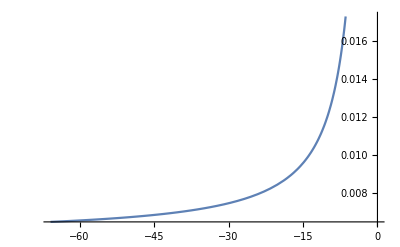

```mathematica
Plot[{FillingFactor[x]}, {x, x10, 0}]
```

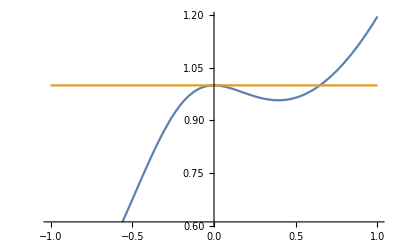

```mathematica
Plot[{FillingFactor[x], y[x]=1}, {x, -1, 1}]
```

```mathematica
NSolve[FillingFactor[x]==1, x]
```

NSolve[1/(1+x^2)2.65342×10^-69 (Piecewise[{{1.56094×10^33 √(1+x^2), -29600000000/219≤x≤-65.8627}, {1/(5.15114×10^-35-x^3/(19413204473948739943955915389918794 (1+x^2)^(3/2))), -0.593256≤x≤1.34953×10^7}, {InterpolatingFunction[{{-65.8627, -0.593256}}, <>][x], -65.8627<x<-0.593256}, {InterpolatingFunction[…][x], 1.34953×10^7<x≤29600000000/219}, {0, True}}])^2==1,x]

```mathematica
Plot[{AreaBH[x], Σhyp[x]}, {x, 0, 1000000},PlotLegends->{"area", "hyp"}, PlotRange->All]
```

-Graphics-

```mathematica
AreaBH[10^8]
```

5.99545×10^27

```mathematica
Σhyp[10^8]
```

6.02035×10^27

```mathematica
FillingFactor[xi]
```

0.0057462

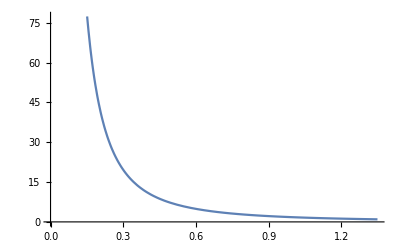

```mathematica
Plot[FillingFactor[x], {x, x011, x012}]
```

```mathematica
FFnorm[x_]:= (M1[x])^2/(m0*(fescala[x])^2)
```

```mathematica
Plot[FFnorm[x], {x, -xi, xi}]
```

-Graphics-